## A Mathematica Notebook for Symbolic Circuit Analysis with gEDA

John Doty
Noqsi Aerospace, Ltd.
www.noqsi.com

This work is Copyright 2007 Noqsi Aerospace, Ltd.
This work is licensed under the Creative Commons Attribution - Share Alike 3.0 License.To view a copy of this license, visit http : // creativecommons.org/licenses/by - sa/3.0/or send a letter to Creative Commons, 171 Second Street, Suite 300, San Francisco, California, 94105, USA.

## Overview

This notebook contains functions for analyzing circuits drawn and netlisted with the gEDA package. For information on gEDA itself, visit http://geda.seul.org. In gEDA, most design flows, including this one, are controlled by "attributes" attached to the symbols in a design. Details of the attributes controlling this design flow are given the following sections of this document. Use this information when you draw your design schematic with gschem.

To obtain a "netlist" that these functions can use, run the shell command:

gnetlist -g mathematica [other options] file.sch ...

The name(s) of your schematic files are the trailing arguments. By default, this produces a file "output.net" containing the Mathematica expressions these functions need as input.

If your gEDA installation lacks the gnetlist back end program gnet-mathematica.scm, you may obtain it from http://www.noqsi.com/ or, most likely, from wherever you obtained this notebook.

## The functions and their usage

Note: you may load these functions either through the Evaluate Initialization Cells menu command, or by loading the file gEDAmath.m.

#### Conventions

Circuit variables are voltages and currents. Voltages are represented as v["netname"] or v["refdes","pinnumber"]. The form v["pinnumber"] also appears in model functions that use modeleqs[] to insert the reference designator in the equations. Currents are represented as i["refdes","pinnumber"]. Reference designators, pin numbers, and network names are quoted to prevent evaluation as they may contain special characters or conflict with built in symbols. Beware that in common output forms Mathematica omits the quotes, but they must appear in input.

In gschem, you may specify models either explicitly with a model= attribute or implicitly by using the device= attribute attached to the component. When using the model= attribute, specify any options as parameters of the model, for example "model=opamp[gain->1000000]". If no options are given, you should still supply an empty pair of [], at least for the model functions defined below. If the model= attribute is present, it takes precedence over other attributes in determining the model.

If the model= attribute is not present, the model will be the value of the device= attribute in lowercase. The options in this case will be a single replacement rule for value. If the value= attribute is present, its value is used (this value may be a symbol or other Mathematica expression). Otherwise, the value of the refdes= attribute, in lowercase, is used, so the capacitor C1 will have value→c1 if not otherwise specified.

#### Model functions

These functions generate model equations from the model specifications in the netlist. A model specification is of the form modelname[args][refdes], for example opamp[gain->1000000]["U2"]. The convention adopted here is that the args form a list of replacement rules, but it is possible to define and use models that don't follow this convention.

In general, an N terminal device model function should return a list of N equations. Often, one of the equations will express that the sum of all the pin currens is zero (Kirchoff's current law), but that is not required, allowing such things as three terminal opamps and one terminal sources.

Model functions may also have side effects: note that testpoint[] equates an alias to a pin voltage.

These functions generate linear algebraic equations in the complex frequency domain. A different set (possibly with the same names) could generate the equations for a different kind of analysis, for example nonlinear differential equations.

modeleqs[] is a helper to insert the refdes in the v[] and i[] variables, making the model functions more readable.

```mathematica
modeleqs[refdes_,eqs___]:={eqs}/.{v[pin_]->v[refdes,pin],i[pin_]->i[refdes,pin]}
```

Three terminal opamp model. Note that this does not obey Kirchoff's current law: there are implicit return currents through ground. The gain equation is organized to put gain and bandwidth in denominators where Mathematica's Infinity heuristics will wipe out the associated  terms instantly when that's what's wanted. The list of substitutions at the end represents defaults: the options in the model specification, if present, take precedence.

```mathematica
opamp[options___][refdes_]:=modeleqs[refdes,v["3"](1/gain+s/(2π bandwidth))==v["1"]-v["2"],i["1"]==bias,i["2"]==bias]/.{options}/.{gain->Infinity,bandwidth->Infinity,bias->0}
```

generalZ[] is a helper for making impedance models. Note that the two equations are Ohm's law and Kirchoff's current law.

```mathematica
generalZ[refdes_,z_]:=modeleqs[refdes,v["1"]-v["2"]==z i["1"],i["1"]+i["2"]==0]
```

Resistors, capacitors, and inductors are special cases of impedances. The value → substitutions are defaults: the options get the first chance to set value.

```mathematica
resistor[options___][refdes_]:=generalZ[refdes,value]/.{options}/.value->r
```

```mathematica
capacitor[options___][refdes_]:=generalZ[refdes,1/(s value)]/.{options}/.value->c
```

```mathematica
inductor[options___][refdes_]:=generalZ[refdes,s value]/.{options}/.value->l
```

A voltage source just fixes the voltage on its pin. Kirchoff gets no say. The voltage is given by the value= attribute and may be a variable or constant.

```mathematica
voltage[options___][refdes_]:={v[refdes,"1"]==value}/.{options}/.value->vin
```

A testpoint is intended to associate a simple variable name with the voltage it's connected to. Draws no current, so has no effect on the circuit. The variable name is its value= attribute.

```mathematica
testpoint[options___][refdes_]:=(Evaluate[value/.{options}/.value->vtest]=v[refdes,"1"];{i[refdes,"1"]==0})
```

#### Solve the circuit equations

Once you've evaluated the contents of a netlist file, you may use solvecircuit[] to obtain the solution of the circuit equations. It returns the solution as a list of rules.

```mathematica
solveCircuit[]:=Solve[Rationalize[Flatten[{nodeEquations,modelEquations}]],variables][[1]]
```

In many cases, the full symbolic solution is not needed. If you've established an input (for example with a voltage model) and an output (for example with a testpoint model) you may use transferFunction[] with the associated variable names as arguments to obtain an expression representing the "transfer function" from input to output.

```mathematica
transferFunction[in_,out_]:=out/in/.solveCircuit[]
```

Establish the "datum" node.

```mathematica
v["GND"]=0;
```

#### Find response versus time symbolically

Given a transfer function as an expression in complex frequency s, it is useful to be able to obtain the response of the circuit to a stimulus as an expression in time t. Unfortunately, this only works in special cases. Use the numerical analysis functions below when these don't work.

tResponse[tf,stim] finds the temporal response of a circuit with transfer function tf (given as an expression in s) with stimulus stim (given as an expression in t).

```mathematica
tResponse[tf_,stim_]:=InverseFourierTransform[(tf/.(s->-ⅈ ω)) FourierTransform[stim,t,ω],ω,t]
```

stepResponse[tf] gives the response to a unit step.

```mathematica
stepResponse[tf_]:=tResponse[tf,HeavisideTheta[t]]
```

impulseResponse[tf] gives the response to a unit impulse.

```mathematica
impulseResponse[tf_]:=tResponse[tf,DiracDelta[t]]
```

#### Find response versus time numerically

While Mathematica's NIntegrate[] function implements stategies designed to blindly evaluate Fourier integrals, they are slow and often suffer from convergence problems. FFT methods work much better here. These are very fast, facilitating numerical optimization of a design.

Note that in these methods time is implicitly cyclic, and there is a little signal leakage backwards in time due to windowing. Thus, a result that has a steep step at t==0 will show a small glitch at the end of the solution (t==tt).

tfdft[tf,dt,n] computes the discrete Fourier transform of the impulse response corresponding to the transfer function tf by sampling tf along the imaginary axis. The number of samples is n and the corresponding time resolution is dt.

```mathematica
tfdft[tf_,dt_,n_]:=RotateLeft[Table[tf/.s->-ⅈ N[(2 π k)/(n dt)],{k,Ceiling[-n/2],Ceiling[n/2]-1}],Floor[n/2]]/(dt √n)
```

Hanning window function. This suppresses some annoying artifacts (Gibbs oscillations) at the price of a small loss in time resolution. You could just set this to 1 if you'd rather have the oscillations.

```mathematica
window[n_]:=Table[0.5(1.0+Cos[2.0Pi k/n]),{k,0,n-1}]
```

impulist returns the impulse response as a list of {time,amplitude} pairs.

```mathematica
timelist[n_,dt_]:=Table[k dt,{k,0,n-1}]
impulist[tf_,dt_,n_]:=Transpose[{timelist[n,dt],InverseFourier[tfdft[tf,dt,n]window[n]]}]
```

impulseResponse[tf,tt,dt] returns the impulse response corresponding to the transfer function tf as an expression in time t. tt is the total time represented by the solution, while dt is the time resolution.

```mathematica
impulseResponse[tf_,tt_,dt_]:=Interpolation[impulist[tf,dt,Ceiling[tt/dt]+1]][t]
```

stepResponse[tf,tt,dt] similarly returns the impulse response corresponding to the transfer function tf as an expression in time t. tt is the total time represented by the solution, while dt is the time resolution.

```mathematica
stepResponse[tf_,tt_,dt_]:=Integrate[impulseResponse[tf,tt,dt],t]
```

## An example

Note: these definitions will not load automatically: you must select and evaluate them to actually compute this example.

Here's the schematic for a pulse shaper:

In this case, I've given resistances in kΩ and bandwidth in MHz. To be consistent, capacitances are then nF and inductances are mH. Time is microseconds.

Here are the contents of the netlist file. Evaluate this cell to finish the construction of the equations. For your own netlists, you can either import the file into a cell as I've done here or use Get[].

```mathematica
v["U3","2"]=v["unnamed_net15"];
v["R9","2"]=v["unnamed_net15"];
v["R17","1"]=v["unnamed_net15"];
v["U3","1"]=v["unnamed_net14"];
v["R16","2"]=v["unnamed_net14"];
v["C15","2"]=v["unnamed_net14"];
v["U4","2"]=v["unnamed_net13"];
v["R19","2"]=v["unnamed_net13"];
v["R20","1"]=v["unnamed_net13"];
v["out","1"]=v["unnamed_net12"];
v["U4","3"]=v["unnamed_net12"];
v["R20","2"]=v["unnamed_net12"];
v["U4","1"]=v["unnamed_net11"];
v["C16","2"]=v["unnamed_net11"];
v["R18","2"]=v["unnamed_net11"];
v["R18","1"]=v["unnamed_net10"];
v["L5","2"]=v["unnamed_net10"];
v["U3","3"]=v["unnamed_net9"];
v["R17","2"]=v["unnamed_net9"];
v["L5","1"]=v["unnamed_net9"];
v["U1","2"]=v["unnamed_net8"];
v["R3","2"]=v["unnamed_net8"];
v["R4","1"]=v["unnamed_net8"];
v["U1","1"]=v["unnamed_net7"];
v["R2","2"]=v["unnamed_net7"];
v["C1","2"]=v["unnamed_net7"];
v["in","1"]=v["unnamed_net6"];
v["C1","1"]=v["unnamed_net6"];
v["U2","2"]=v["unnamed_net5"];
v["R6","2"]=v["unnamed_net5"];
v["R7","1"]=v["unnamed_net5"];
v["U2","3"]=v["unnamed_net4"];
v["C15","1"]=v["unnamed_net4"];
v["R7","2"]=v["unnamed_net4"];
v["R16","1"]=v["GND"];
v["R9","1"]=v["GND"];
v["R19","1"]=v["GND"];
v["C16","1"]=v["GND"];
v["R2","1"]=v["GND"];
v["R3","1"]=v["GND"];
v["R6","1"]=v["GND"];
v["C2","1"]=v["GND"];
v["U2","1"]=v["unnamed_net3"];
v["C2","2"]=v["unnamed_net3"];
v["R5","2"]=v["unnamed_net3"];
v["R5","1"]=v["unnamed_net2"];
v["L1","2"]=v["unnamed_net2"];
v["U1","3"]=v["unnamed_net1"];
v["R4","2"]=v["unnamed_net1"];
v["L1","1"]=v["unnamed_net1"];
nodeEquations={
i["U3","2"]+i["R9","2"]+i["R17","1"]==0,
i["U3","1"]+i["R16","2"]+i["C15","2"]==0,
i["U4","2"]+i["R19","2"]+i["R20","1"]==0,
i["out","1"]+i["U4","3"]+i["R20","2"]==0,
i["U4","1"]+i["C16","2"]+i["R18","2"]==0,
i["R18","1"]+i["L5","2"]==0,
i["U3","3"]+i["R17","2"]+i["L5","1"]==0,
i["U1","2"]+i["R3","2"]+i["R4","1"]==0,
i["U1","1"]+i["R2","2"]+i["C1","2"]==0,
i["in","1"]+i["C1","1"]==0,
i["U2","2"]+i["R6","2"]+i["R7","1"]==0,
i["U2","3"]+i["C15","1"]+i["R7","2"]==0,
i["U2","1"]+i["C2","2"]+i["R5","2"]==0,
i["R5","1"]+i["L1","2"]==0,
i["U1","3"]+i["R4","2"]+i["L1","1"]==0};
modelEquations={
voltage[value->in]["in"],
resistor[value->rg]["R17"],
resistor[value->1]["R5"],
resistor[value->1]["R16"],
resistor[value->rg]["R4"],
resistor[value->1]["R3"],
testpoint[value->out]["out"],
resistor[value->1]["R2"],
inductor[value->l1]["L1"],
capacitor[value->c16]["C16"],
capacitor[value->c2]["C2"],
model=opamp[gain->1000000,bandwidth->9]["U4"],
resistor[value->1]["R9"],
capacitor[value->c15]["C15"],
capacitor[value->c1]["C1"],
model=opamp[gain->1000000,bandwidth->9]["U3"],
model=opamp[gain->1000000,bandwidth->9]["U2"],
resistor[value->1]["R19"],
resistor[value->rg]["R20"],
resistor[value->rg]["R7"],
model=opamp[gain->1000000,bandwidth->9]["U1"],
resistor[value->1]["R18"],
inductor[value->l5]["L5"],
resistor[value->1]["R6"]};
variables={
v["unnamed_net15"],
v["unnamed_net14"],
v["unnamed_net13"],
v["unnamed_net12"],
v["unnamed_net11"],
v["unnamed_net10"],
v["unnamed_net9"],
v["unnamed_net8"],
v["unnamed_net7"],
v["unnamed_net6"],
v["unnamed_net5"],
v["unnamed_net4"],
v["unnamed_net3"],
v["unnamed_net2"],
v["unnamed_net1"],
i["U3","2"],
i["R9","2"],
i["R17","1"],
i["U3","1"],
i["R16","2"],
i["C15","2"],
i["U4","2"],
i["R19","2"],
i["R20","1"],
i["out","1"],
i["U4","3"],
i["R20","2"],
i["U4","1"],
i["C16","2"],
i["R18","2"],
i["R18","1"],
i["L5","2"],
i["U3","3"],
i["R17","2"],
i["L5","1"],
i["U1","2"],
i["R3","2"],
i["R4","1"],
i["U1","1"],
i["R2","2"],
i["C1","2"],
i["in","1"],
i["C1","1"],
i["U2","2"],
i["R6","2"],
i["R7","1"],
i["U2","3"],
i["C15","1"],
i["R7","2"],
i["R16","1"],
i["R9","1"],
i["R19","1"],
i["C16","1"],
i["R2","1"],
i["R3","1"],
i["R6","1"],
i["C2","1"],
i["U2","1"],
i["C2","2"],
i["R5","2"],
i["R5","1"],
i["L1","2"],
i["U1","3"],
i["R4","2"],
i["L1","1"]};
```

As we've got a voltage device in and a testpoint device out, we can obtain the transfer function. Note that it is given in terms of the exact numbers that Mathematica's algebraic algorithms need for reliability.

```mathematica
ShaperTF=transferFunction[in,out]
```

(6561000000000000000000000000 c1 c15 π^4 (1+rg)^4 s^2)/((1+c1 s) (1+c15 s) (9000009 π+9 π rg+500000 s+500000 rg s)^4 (1+c2 s+c2 l1 s^2) (1+c16 s+c16 l5 s^2))

This compact, easily manipulated abstract representation of what the circuit does is what this package is about. We can now very quickly get the step response:

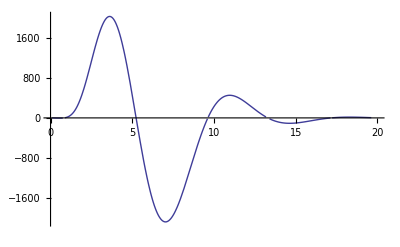

```mathematica
Plot[Evaluate[stepResponse[ShaperTF/.{c1->1,c2->1,c15->1,c16->1,l1->1,l5->1,rg->10},20,.05]],{t,0,20}]
```

That's a sensible step response for a six pole two zero shaping amplifier. But it's not quite what I want. Suppose my requirements are:

1. Positive peak height in the range 1000-1500.
2. No ringing after the negative peak.
3. Settling in 10μs.
4. Positive peak width as large as possible.
5. Standard component values.

To reduce ringing and speed settling, reduce the inductors, increasing bandwidth while reducing Q. Reducing rg reduces gain. Reducing C1 or C15 also speeds things. It only took a minute or so of fiddling to get the following:

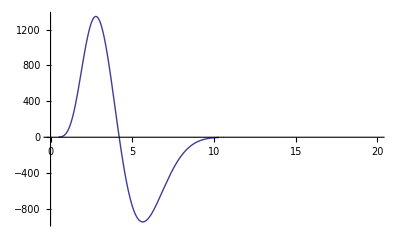

```mathematica
Plot[Evaluate[stepResponse[ShaperTF/.{c1->1,c2->1,c15->.82,c16->1,l1->0.47,l5->0.47,rg->9.1},20,.05]],{t,0,20}]
```

Good enough for my purposes. Automated optimization "is left as an excercise for the reader". It's too easy to tweak by hand when a new plot takes <1 second.

## Implementation Notes

### Security

The gnetlist back end that generates the circuit equations and model invocations does not currently place restrictions on the Mathematica expressions that you may use. Since Mathematica will evaluate any input expression and has all the power of a command shell built in, it is possible that it may evaluate malicious code embedded in a symbol or schematic. If you obtain symbols, schematics, or netlists from a third party, you should beware. It is a good idea to inspect the netlist before feeding it to Mathematica.

A future version of the gnetlist back end may restrict the Mathematica symbols you may use to prevent this from becoming a problem.